Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

Set::write: Tag Times in 0 Null is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

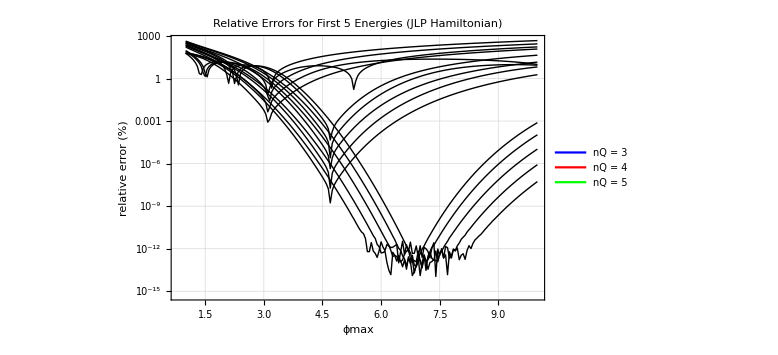

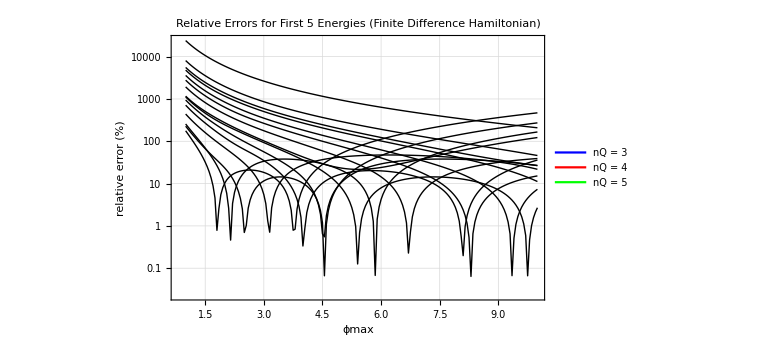

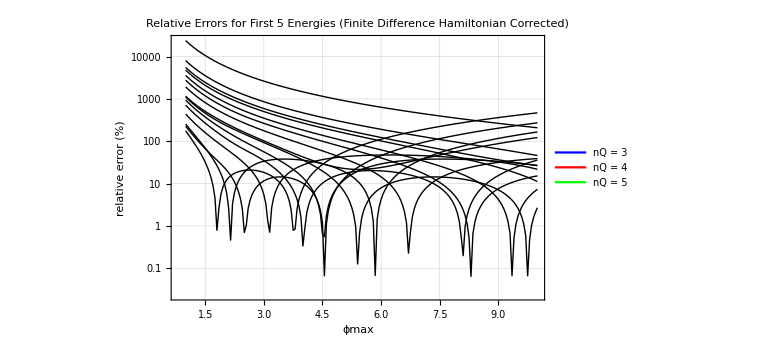

Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

Set::write: Tag Times in 0 Null is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

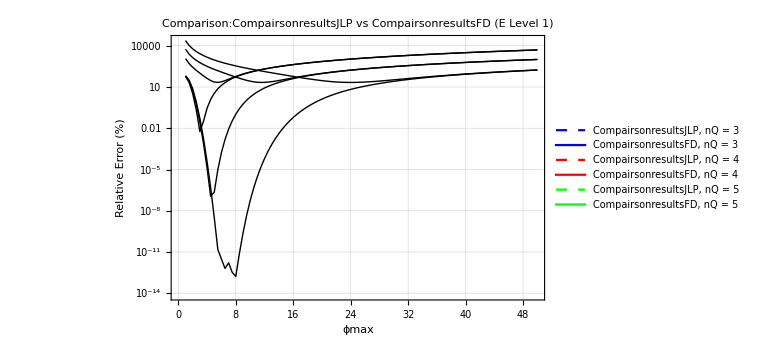

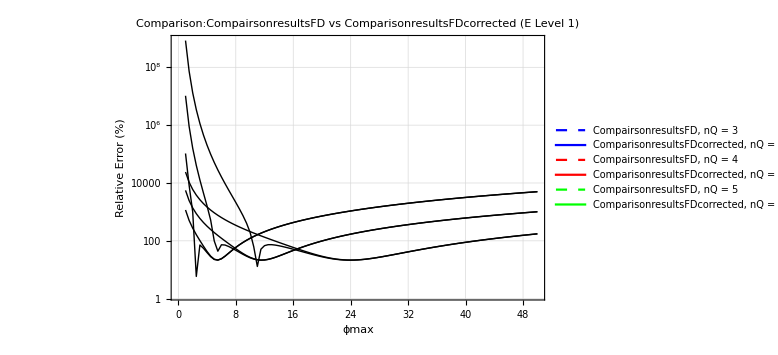

Part::partd: Part specification Missing[KeyAbsent,3]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Missing[KeyAbsent,3]⟦1,2,1⟧ is longer than depth of object.

Part::partd: Part specification Missing[KeyAbsent,3]⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

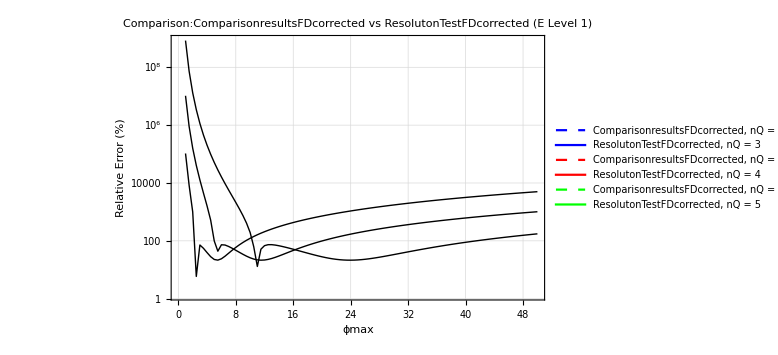

```mathematica
(*Hamiltonian using QuFoTr*)
HamiltonianJLP[ns_,phiMax_]:=Module[
{deltaPhi,beta,phi,phi2,kmax,deltaK,betak,k,F,Pik2,Piphi2,H},

(*each of the phi and pi matricies (position and momentum equivalents) and diagonal in their own space,we apply the QuFoTr to the matricies to move back and forth*)

deltaPhi=2 phiMax/(ns-1);
beta=Range[0,ns-1];
phi=-phiMax+beta deltaPhi;
phi2=DiagonalMatrix[phi^2];(*diagonal phi squared matrix in the field space*)

kmax=Pi/deltaPhi;
deltaK=2 Pi/(deltaPhi ns);
betak=Range[1,ns];
k=-kmax+betak deltaK;

F=Exp[-I Outer[Times,k,phi]]/Sqrt[ns]; (*creates a unitary Fourier matrix that transforms between the field basis and the momentum basis F phi=K*)

Pik2=DiagonalMatrix[k^2];(*diagonal pi squared matrix in momentum space*)

Piphi2=ConjugateTranspose[F].Pik2.F;(*pi squared matrix in field space*)

H=0.5 (phi2+Piphi2);(*Hamiltonian*)
(*might end up being slightly none hermitian because computers so:*)
H=0.5 (H+ConjugateTranspose[H]);

{H,phi}
];

(*Finite-Difference*)

HamiltonianFD[ns_,phiMax_]:=Module[
{deltaPhi,beta,phi,phi2,lap,Piphi2,H},

deltaPhi=2 phiMax/(ns-1);
beta=Range[0,ns-1];
phi=-phiMax+beta deltaPhi;

phi2=DiagonalMatrix[phi^2];(*diagonal phi squared matrix in the field space*)

(*Finite-difference kinetic-energy operator*)
lap=ConstantArray[0,{ns,ns}]; (*empty matrix*)
Do[
lap[[i,i]]=2;(*makes diagonal elements 2*)
lap[[i,Mod[i,ns]+1]]=-1;(*sets elements to the right of the diagonal to -1*)
lap[[Mod[i-2,ns]+1,i]]=-1; (*sets elements to the left of the diagonal to -1*),
{i,ns}];
lap=lap/(deltaPhi^2);(*divide by δφ.b2*)

Piphi2=lap;

(*Hamiltonian*)
H=0.5 (phi2+Piphi2);
H=0.5 (H+ConjugateTranspose[H]);(*ensure Hermitian*)
{H,phi}];

HamiltonianFDCorrected[ns_,phiMax_]:=Module[
{deltaPhi,beta,phi,phi2,lap,Piphi2,H},

deltaPhi=2 phiMax/(ns-1); (*introducing deltaScaling allows me to test how resolutions affects FD*)
beta=Range[0,ns-1];
phi=-phiMax+beta deltaPhi;

phi2=DiagonalMatrix[phi^2];(*diagonal phi squared matrix in the field space*)

(*Finite-difference kinetic-energy operator*)
lap=ConstantArray[0,{ns,ns}]; (*empty matrix*)
Do[
lap[[i,i]]=2;(*makes diagonal elements 2*)
lap[[i,Mod[i,ns]+1]]=-1;(*sets elements to the right of the diagonal to -1*)
lap[[Mod[i-2,ns]+1,i]]=-1; (*sets elements to the left of the diagonal to -1*),
{i,ns}];
lap=lap/(deltaPhi^2);(*divide by δφ.b2*)

Piphi2=lap;

(*Hamiltonian*)
H=0.5 (phi2+Piphi2) +1/24 Power[deltaPhi,2] MatrixPower[Piphi2,4];
H=0.5 (H+ConjugateTranspose[H]);(*ensure Hermitian*)
{H,phi}
];


(*Precision Function*)

FindPrecision[method_,ns_,phiMax_]:=Module[
{H,ordereig,eiglow,eigexact,relerror},(*choose Hamiltonian type based on method*)

{H,_}=Which[method=="FD",HamiltonianFD[ns,phiMax],method == "JLP", HamiltonianJLP[ns,phiMax], method == "FDcorrected", HamiltonianFDCorrected[ns, phiMax], True, Return[$Failed, Module]];
ordereig=Sort[Re[Eigenvalues[H]]];
eiglow=ordereig[[1;;Min[5,Length[ordereig]]]];(*gets five lowest eigenvalues of hamiltonian like in savage*)
eigexact=Range[0,4]+0.5;(*gets exact HO energies*)
relerror=Abs[(eiglow-eigexact)/eigexact]*100;
relerror];


(*Automated results get*)

ComputeResults[method_,nqList_,phiMaxValues_]:=Module[
{results=Association[],ns},
Do[ns=2^nq;
results[nq]=Table[{phiMax,FindPrecision[method,ns,phiMax]},{phiMax,phiMaxValues}];,
{nq,nqList}];(*loops over each nq in nqlist based on the chosen method*)
results];

(*Plotting Functions*)

PlotResults[results_,title_String:"Relative Errors for First 5 Energies (JLP Hamiltonian)"]:=Module[
{plotGroups,colorList,allCurves,legendLabels,plt},

plotGroups=Table[Table[Table[(*still dont really get why I had to do table 3 times*)
{results[nq][[i,1]],results[nq][[i,2,j]]},{i,Length[results[nq]]}],{j,5}],
{nq,nqList} ];(*loops over each nq in the nq list for each of the errors in each energy level*)

colorList={Blue,Red,Green};(*colours*)

allCurves= Flatten[Table[Table[Style[Table[(*know why I need flatten and style but why I need three table things is beyond me*)
{results[nqList[[m]]][[i,1]],results[nqList[[m]]][[i,2,j]]},{i,Length[results[nqList[[m]]]]}],colorList[[m]],Thick],{j,5}],(*j loops over the nq indicies (energy levels)*){m,Length[nqList]}],1 (*again iteration stuff*)];

legendLabels=Table["nQ = "<>ToString[nqList[[m]]],{m,Length[nqList]}];(*makes the legend labels*)

plt=ListLogPlot[allCurves,(*plots as log log graph and which data to plot*)
Joined->True,(*should the data be connected with lines*)
Frame->True,(*Full Frame instead of standard axis*)
FrameLabel->{"ϕmax","relative error (%)"},(*axis labels*)
PlotLegends->Placed[LineLegend[colorList,legendLabels,LegendMarkerSize->30],Below],(*adds legend with labels and size and colour*)
GridLines->Automatic,(*Background gridlines*)
PlotLabel->Style[title,16],(*title*)
ImageSize->Large,PlotRange->All];(*makes sure all of the data is included*)

plt];


SetAttributes[CompareResults,HoldAll];

CompareResults[results1_,results2_,nqList_,level_:1]:=Module[(*'level' lets you pick which energy level to plot*)
{colorList,style1,style2,allCurves,legendLabels,plt, name1, name2},

name1 = SymbolName[Unevaluated[results1]];
name2 = SymbolName[Unevaluated[results2]];

colorList={Blue,Red,Green} ;(*colours for nQ values*)
style1=Table[{colorList[[i]],Thick,Dashed},{i,Length[colorList]}];(*Different styles for each method—same color,different dashing*)
style2=Table[{colorList[[i]],Thick,Solid},{i,Length[colorList]}];

(*Section off results for JLP and FD, one energy level per nq*)
allCurves=Flatten[Table[
{Style[Table[{results1[nqList[[m]]][[i,1]],(*phi max*)
results1[nqList[[m]]][[i,2,level]]}, (*relative error for for chosen energy level *)
{i,Length[results1[nqList[[m]]]]}], (*loops through results*)
Sequence@@style1[[m]]],(*picks the style for those results*)
Style[Table[{results2[nqList[[m]]][[i,1]],
results2[nqList[[m]]][[i,2,level]]},
{i,Length[results2[nqList[[m]]]]}],
Sequence@@style2[[m]]]} ,

{m,Length[nqList]}],1];(*loops through nqs*)

(*Legend labels*)
legendLabels=Flatten@Table[{name1<>", nQ = "<>ToString[nqList[[m]]],name2<>", nQ = "<>ToString[nqList[[m]]]},{m,Length[nqList]}];

plt=ListLogPlot[allCurves,Joined->True,Frame->True,FrameLabel->{"ϕmax","Relative Error (%)"},(*Plot the results*)PlotLegends->Placed[LineLegend[Flatten@Table[{Directive[Sequence@@style1[[m]]],Directive[Sequence@@style2[[m]]]},{m,Length[nqList]}],
legendLabels,LegendMarkerSize->30],Below],
GridLines->Automatic,
PlotLabel->Style["Comparison:"<>name1<>" vs "<>name2<>" (E Level "<>ToString[level]<>")",16],
ImageSize->Large,PlotRange->All];
plt];

(*Parameters and results*)

nqList={3,4,5};
phiMaxValues=Range[1,10,0.05];

resultsJLP=ComputeResults["JLP",nqList,phiMaxValues];
resultsFD=ComputeResults["FD",nqList,phiMaxValues ];
resultsFDcorrected=ComputeResults["FDcorrected",nqList,phiMaxValues];

(*creates the individual plots*)
plotJLP=PlotResults[resultsJLP,"Relative Errors for First 5 Energies (JLP Hamiltonian)"];
plotFD=PlotResults[resultsFD,"Relative Errors for First 5 Energies (Finite Difference Hamiltonian)"];
plotFDcorrected = PlotResults[resultsFD,"Relative Errors for First 5 Energies (Finite Difference Hamiltonian Corrected)"];

(*Display individual plots*)
plotJLP
plotFD
plotFDcorrected

(*comparison plots*)

CompairsonphiMaxValues=Range[1,50,0.5];
CompairsonresultsJLP=ComputeResults["JLP",nqList,CompairsonphiMaxValues];
CompairsonresultsFD=ComputeResults["FD",nqList,CompairsonphiMaxValues ];
ComparisonresultsFDcorrected = ComputeResults["FDcorrected",nqList,CompairsonphiMaxValues];

plotComparisonGround=CompareResults[CompairsonresultsJLP,CompairsonresultsFD,nqList,1];
plotComparisonGround

plotFDcomparison = CompareResults[CompairsonresultsFD,ComparisonresultsFDcorrected,nqList,1];
plotFDcomparison
```